```mathematica
(* Backward Euler *)
```

```mathematica
bE[f_,dt_,T_,init_] := Module[{ret = {{0.0,init}},y=init,t=0.0,numsteps=T/dt},Do[y=ynew/.Solve[ynew == y+dt*f[ynew,t+dt],ynew][[1]]; 
t= t+dt;
ret = Append[ret,{t,y}],{i,1,numsteps}];ret];
```

```mathematica
(* Forward Euler *)
fE[f_,dt_,T_,init_]:=Module[{ret={{0.0,init}},y=init,t=0.0,numsteps=T/dt},
Do[y=y+dt*f[y,t]; t = t+dt;
ret=Append[ret,{t,y}],{i,1,numsteps}];ret];
```

```mathematica
(* Adams-Bashforth 2-step *)
```

```mathematica
aB[f_,dt_,T_,init_]:=Module[{ret={{0.0,init}},y1=init,y2,y,t=0.0,numsteps=T/dt},
Do[y2 = y1 + (3/2)*dt*f[y1,t]-(dt/2)*f[y,t-dt];
y=y1;
y1=y2;
t=t+dt;ret = Append[ret,{t,y2}],{i,1,numsteps}];ret];
```

```mathematica
(* Ex 1: f' = 2-2f+ Exp(-4t), f(0) = 1.
	Analytical Sol: f(t) = 1+ 1/2 Exp(-2t) -1/2 Exp(-4t)
	Each Numerical Solution has a step size h=0.1 and is calculated over domain (0,3).*)
```

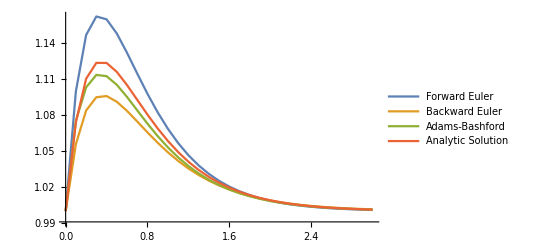

```mathematica
f[y_,t_] = 2-2y+Exp[-4t];
retaB = aB[f,0.1,3,1];
retfE = fE[f,0.1,3,1];
retbE = bE[f,0.1,3,1];
sol = Transpose[{Range[0,3,.1],Table[1+1/2Exp[-2t]-1/2Exp[-4t],{t,0,3,.1}]}];
soly = Transpose[{ConstantArray[0,Length[sol]],Table[1+1/2Exp[-2t]-1/2Exp[-4t],{t,0,3,.1}]}];
ListLinePlot[{retfE,retbE,retaB,sol},PlotLegends->{"Forward Euler","Backward Euler","Adams-Bashford","Analytic Solution"}]
```

```mathematica
(* Log Plot of Error for each Method *)
```

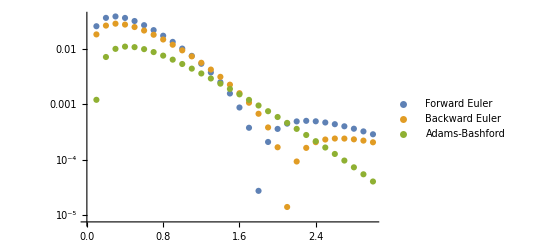

```mathematica
ListLogPlot[{Abs[retfE-soly],Abs[retbE-soly],Abs[retaB-soly]},PlotLegends->{"Forward Euler","Backward Euler","Adams-Bashford"}]
```

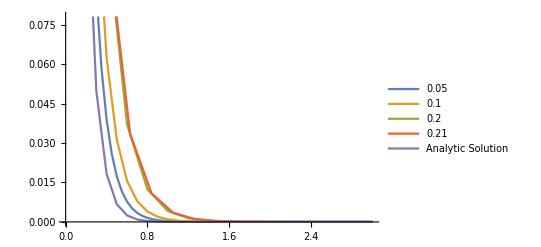

```mathematica
(* Ex 2: y' = -10y, y(0) = 1 
	Solved Numerically with Backwards Euler in different step sizes*)
ode [y_,t_] = -10y;
besol005  = bE[ode,0.05,3,1];
besol01 = bE[ode,0.1,3,1];
besol02 = bE[ode,0.2,3,1];
besol021 = bE[ode,0.21,3,1];
ansol = Transpose[{Range[0,3,.1],Table[Exp[-10t],{t,0,3,.1}]}];
ListLinePlot[{besol005,besol01,besol02,besol021,ansol},PlotLegends->{"0.05","0.1","0.2","0.21","Analytic Solution"}]
```

```mathematica
(* Log Plot of Error per Step Size*)
```

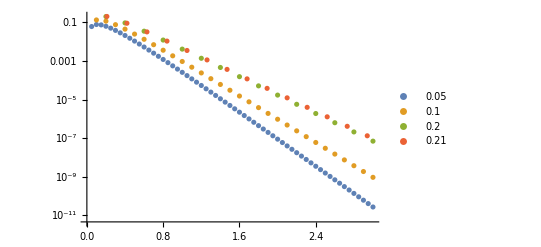

```mathematica
ansoly1 =Transpose[{ConstantArray[0,Length[besol005]],Table[Exp[-10t],{t,0,3,0.05}]}];
ansoly2 = Transpose[{ConstantArray[0,Length[besol01]],Table[Exp[-10t],{t,0,3,0.1}]}];
ansoly3 = Transpose[{ConstantArray[0,Length[besol02]],Table[Exp[-10t],{t,0,3,0.2}]}];
ansoly4 = Transpose[{ConstantArray[0,Length[besol021]],Table[Exp[-10t],{t,0,3,0.21}]}];
ListLogPlot[{Abs[besol005-ansoly1],Abs[ansoly2-besol01],Abs[ansoly3-besol02],Abs[besol021-ansoly4]},PlotLegends->{"0.05","0.1","0.2","0.21"}]
```

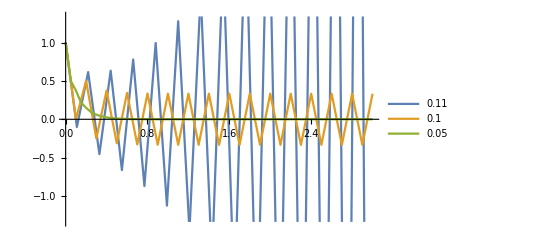

```mathematica
(* Can we solve this ODE with an Adams-Bashforth method? *)
absol1= aB[ode,0.1,3,1];
absol2=aB[ode,0.05,3,1];
absol3 = aB[ode,0.11,3,1];
ListLinePlot[{absol3,absol1,absol2},PlotLegends->{"0.11","0.1","0.05"}]
```

```mathematica
(* Only if we use a small enough step size h <0.1*)
```